# Numerical holography using Mathematica

## Exercise 1. Schwarschild black brane, Eddington-Finkelstein coordinates. (Easy)

### A. Load Riemannian geometry code

Load the exterior derivative, Riemannian geometry, and tensor calculus package EDCRGTCcode.m.  If this is not in your Mathematica search path, you can fetch the file from here.  Also fetch the documentation notebook RGTC.nb and quickly read the sections 1.0 and 1.1.

```mathematica
<<EDCRGTCcode.m
```

### B. Compute the geometry resulting from the line element ds^2=2dt (dr-A(r)dt) + (r^2/L^2)(dx^2+dy^2+dz^2).

To do so, define an array (i.e., list) coords of the five symbols which represent your coordinate variables and a symmetric matrix ansatz containing the metric coefficients corresponding to the above line element.  Then run RGtensors with ansatz and coords as arguments.  (Starting with Clear[A]; is recommended, so that you can rerun this section, if desired, without being affected by subsequent definitions of the function A.)

```mathematica
Clear[A];
coords={t,x,y,z,r};
ansatz = DiagonalMatrix[{-2A[r],r^2/L^2,r^2/L^2,r^2/L^2,0}];
ansatz[[1,5]]=ansatz[[5,1]]=1;
RGtensors[ansatz,coords];
```

gdd = (-2 A[r] | 0 | 0 | 0 | 1
0 | r^2/L^2 | 0 | 0 | 0
0 | 0 | r^2/L^2 | 0 | 0
0 | 0 | 0 | r^2/L^2 | 0
1 | 0 | 0 | 0 | 0)

LineElement = 2 d[r] d[t]-2 A[r] d[t]^2+(r^2 d[x]^2)/L^2+(r^2 d[y]^2)/L^2+(r^2 d[z]^2)/L^2

gUU = (0 | 0 | 0 | 0 | 1
0 | L^2/r^2 | 0 | 0 | 0
0 | 0 | L^2/r^2 | 0 | 0
0 | 0 | 0 | L^2/r^2 | 0
1 | 0 | 0 | 0 | 2 A[r])

gUU computed in 0.003454 sec

Gamma computed in 0.004646 sec

Riemann(dddd) computed in 0.010659 sec

Riemann(Uddd) computed in 0.006743 sec

Ricci computed in 0.002854 sec

Weyl computed in 0.020452 sec

Einstein computed in 0.00301 sec

### C. Write out the components of the Einstein field equations with a cosmological constant Λ = -6/L^2.

The Einstein equations with a cosmological constant are E_MN+ Λ g_MN=0, where E_MN = R_MN- 1/2 R g_MN is the Einstein tensor.  For later convenience, define Einstein as the set of (left hand sides of the) field equations using a delayed assignment, that is Einstein := ..., so that it will be easy to re-evalute the field equations below with a perturbed metric.  By looking at the components of Einstein, you should see that the “redshift” function A(r) must satisfy two diiferent differential equations, one of which is -6/L^2+3(2A(r)+r A'(r))/r^2=0.  What is the other equation for A(r) which emerges?  Is this an independent condition on A(r)?

```mathematica
Lambda=-6/L^2;
Einstein:=EUd + Lambda IdentityMatrix[5];
Einstein
```

{{-6/L^2+(3 (2 A[r]+r A'[r]))/r^2,0,0,0,0},{0,-6/L^2+(2 A[r]+4 r A'[r]+r^2 A''[r])/r^2,0,0,0},{0,0,-6/L^2+(2 A[r]+4 r A'[r]+r^2 A''[r])/r^2,0,0},{0,0,0,-6/L^2+(2 A[r]+4 r A'[r]+r^2 A''[r])/r^2,0},{0,0,0,0,-6/L^2+(3 (2 A[r]+r A'[r]))/r^2}}

The second order equation is a linear combination of the first order equation and its radial derivative:

```mathematica
Einstein[[2,2]]- Einstein[[1,1]] - 1/3 r D[Einstein[[1,1]],r]//Simplify
```

0

### D. Find the most general solution for the redshift function A(r).

Use DSolve.

```mathematica
DSolve[Einstein[[1,1]]==0,A[r],r]
```

{{A[r]→r^2/(2 L^2)+C[1]/r^2}}

### E. Define A as a pure function.

A pure function is most easily defined using a style like ff = # + #^2-#^3&, where #  represents the function argument, and & indicates the end of the function definition.  (For functions with multiple arguments, one uses #1, #2, etc.)  One can also use Function. Using pure functions is often faster, and more convenient than using pattern matching definitions (e.g., gg[r_] = r + r^2-r^3).

Use -1/2 m L^2 as the coefficient of the r^-2 term in A(r) (instead of something like C[1]).  Re-evaluate Einstein and verify that the field equations are satisfied.

```mathematica
A = 1/2 #^2/L^2-1/2m L^2/#^2&;
Einstein//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### F. Define the horizon radius rh as the positive, real root of A(r).

You can, of course, solve for the root by hand (or by inspection), but using Solve is recommended.  Using Mathematica to verify things you can equally well do by hand is often helpful as a simple strategy to avoid typos and trivial mistakes.

```mathematica
Solve[A[r]==0,r]
rh=(r/.%[[4]])
```

{{r→-L m^(1/4)},{r→-ⅈ L m^(1/4)},{r→ⅈ L m^(1/4)},{r→L m^(1/4)}}

L m^(1/4)

### G. Find the Hawking temperature, equal to (2π)^-1times the slope of A(r) at the horizon.

Define a substitution msub which will express m in terms of the temperature T.

```mathematica
Temp=A'[r]/(2Pi)/.r->rh
msub=Solve[Temp==T,m][[1]]
```

m^(1/4)/(L π)

{m→L^4 π^4 T^4}

## Exercise I1. Quasinormal mode equation (spin-2 channel). (Easy/Medium)

### A. Add an infinitesimal plane wave perturbation to the metric, δg_xy=η e^(i(q z - ω t))(r^2/L^2)f(r) + O(η^2), with η a formal expansion parameter. Rerun RGtensors to compute the perturbed geometry.

Asymptotic expansions are easily entered in Mathematica using O[x]^n to denote terms which vanish as x^n as x goes to 0.  Conveniently, the RGTC package allows the metric coefficients to be given by an asymptotic expansion.

If necessary, re-load the RGTC package and re-enter the definitions of coords, ansatz, Einstein, A, rh, and msub.  Then add the perturbation to ansatz and re-run RGtensors.

```mathematica
ansatz[[2,3]]=ansatz[[3,2]]=η E^(I (q z-ω t))(r^2/L^2)f[r]+O[η]^2;
RGtensors[ansatz,coords];
```

gdd = (-2 (-(L^2 m)/(2 r^2)+r^2/(2 L^2)) | 0 | 0 | 0 | 1
0 | r^2/L^2 | (ⅇ^(ⅈ (q z-t ω)) r^2 f[r] η)/L^2+O[η]^2 | 0 | 0
0 | (ⅇ^(ⅈ (q z-t ω)) r^2 f[r] η)/L^2+O[η]^2 | r^2/L^2 | 0 | 0
0 | 0 | 0 | r^2/L^2 | 0
1 | 0 | 0 | 0 | 0)

LineElement = (2 d[r] d[t]+((L^4 m-r^4) d[t]^2)/(L^2 r^2)+(r^2 d[x]^2)/L^2+(r^2 d[y]^2)/L^2+(r^2 d[z]^2)/L^2)+(2 ⅇ^(ⅈ q z-ⅈ t ω) r^2 d[x] d[y] f[r] η)/L^2+O[η]^2

gUU = (0 | 0 | 0 | 0 | 1+O[η]^3
0 | L^2/r^2+(ⅇ^(2 ⅈ q z-2 ⅈ t ω) L^2 f[r]^2 η^2)/r^2+O[η]^3 | -(ⅇ^(ⅈ q z-ⅈ t ω) L^2 f[r] η)/r^2+O[η]^2 | 0 | 0
0 | -(ⅇ^(ⅈ q z-ⅈ t ω) L^2 f[r] η)/r^2+O[η]^2 | L^2/r^2+(ⅇ^(2 ⅈ q z-2 ⅈ t ω) L^2 f[r]^2 η^2)/r^2+O[η]^3 | 0 | 0
0 | 0 | 0 | L^2/r^2+O[η]^3 | 0
1+O[η]^3 | 0 | 0 | 0 | -(L^4 m-r^4)/(L^2 r^2)+O[η]^3)

gUU computed in 0.015359 sec

Gamma computed in 0.080111 sec

Riemann(dddd) computed in 0.279559 sec

Riemann(Uddd) computed in 0.625641 sec

Ricci computed in 0.276419 sec

Weyl computed in 0.772194 sec

Einstein computed in 0.067148 sec

### B. Examine the first order corrections to Einstein equations, and extract the linear quasinormal mode (QNM) equation which the radial function f(r) must satisfy.

Define QNMeqn as this equation.  Show that it equals (or is equivalent to):

(L^2 (L^2 q^2+3 ⅈ r ω) f[r])/r^4+((L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r])/r^5+((L^4 m-r^4) f''[r])/r^4

```mathematica
Einstein+O[η]^2//Simplify
Normal[%]
QNMeqn=2 L^2 r^-2 Coefficient[%[[2,3]],E^(I(q z - ω t))η]//Collect[#,{f[r],f'[r],f''[r]}]&//Map[Simplify,#,{1}]&
```

{{O[η]^2,O[η]^2,O[η]^2,O[η]^2,O[η]^2},{O[η]^2,O[η]^2,1/(2 L^2 r^3)ⅇ^(ⅈ (q z-t ω)) (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r]) η+O[η]^2,O[η]^2,O[η]^2},{O[η]^2,1/(2 L^2 r^3)ⅇ^(ⅈ (q z-t ω)) (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r]) η+O[η]^2,O[η]^2,O[η]^2,O[η]^2},{O[η]^2,O[η]^2,O[η]^2,O[η]^2,O[η]^2},{O[η]^2,O[η]^2,O[η]^2,O[η]^2,O[η]^2}}

{{0,0,0,0,0},{0,0,1/(2 L^2 r^3)ⅇ^(ⅈ (q z-t ω)) η (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r]),0,0},{0,1/(2 L^2 r^3)ⅇ^(ⅈ (q z-t ω)) η (L^2 r (L^2 q^2+3 ⅈ r ω) f[r]+(L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r]+r (L^4 m-r^4) f''[r]),0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

(L^2 (L^2 q^2+3 ⅈ r ω) f[r])/r^4+((L^4 m-5 r^4+2 ⅈ L^2 r^3 ω) f'[r])/r^5+((L^4 m-r^4) f''[r])/r^4

### C. Try using DSolve to solve the QNM equation analytically --- and get a useless answer.

```mathematica
DSolve[QNMeqn==0,f[r],r]
```

{{f[r]→DifferentialRoot[Function[{y,x},{-x L^2 (L^2 q^2+3 ⅈ x ω) y[x]+(5 x^4-L^4 m-2 ⅈ x^3 L^2 ω) y'[x]+(x^5-x L^4 m) y''[x]==0,y[1]==C[1],y'[1]==C[2]}],«»][r]}}

Yep, useless

### D. The point r = rh is a regular singular point of the QNM equation. Explain why.

Because the coefficient of the leading f’’ derivative term vanishes at rh (without corresponding zeros in the other coefficients).

### E. Find the local behavior of solutions near r = rh. Which solution represents an outgoing wave at the horizon?

Try f(r) ~ (δr)^γ [1 + O(δr)), with δr = r-rh.

```mathematica
QNMeqn/.r->rh+δr/.f->((#-rh)^γ g[#-rh]&)
%/.g->(1+O[#]&)//Simplify
Solve[Normal[%] δr^-γ==0,γ]
```

(L^2 δr^γ (L^2 q^2+3 ⅈ (L m^(1/4)+δr) ω) g[δr])/((L m^(1/4)+δr)^4)+((L^4 m-5 (L m^(1/4)+δr)^4+2 ⅈ L^2 (L m^(1/4)+δr)^3 ω) (γ δr^(-1+γ) g[δr]+δr^γ g'[δr]))/((L m^(1/4)+δr)^5)+((L^4 m-(L m^(1/4)+δr)^4) ((-1+γ) γ δr^(-2+γ) g[δr]+2 γ δr^(-1+γ) g'[δr]+δr^γ g''[δr]))/((L m^(1/4)+δr)^4)

δr^γ ((2 γ (-(2 m^(1/4) γ)/L+ⅈ ω))/(√m δr)+O[δr]^0)

{{γ→0},{γ→(ⅈ L ω)/(2 m^(1/4))}}

The second solution (with imaginary exponent) is outgoing, since the complete eigenfunction behaves as exp[-i ω (t - (L m^(-1/4)/2) ln(δr))], showing that as t increases, constant phase surfaces move outward (i.e., keeping the phase constant requires increasing δr).

### F. The point r = ∞, at the boundary of the spacetime, is also a regular singular point. Why?

Because if you rewrite the equation in terms of an inverted radial coordinate, u = 1/r, (and cancel an overall factor of u^2), then the linear operator has the form u^2∂_u +u∂_u +const. as u goes to zero, and once again the coefficient of the leading derivative vanishes.

### G. Find the local behavior of solutions near r = ∞. Which solution represents a change in the boundary metric, and which represents a perturbation to the stress-tensor expectation value?

Try f(r) ~ r^-γ (1 + O(1/r)).

```mathematica
QNMeqn/.r->1/u/.f->(#^-γ g[1/#]&)
%/.g->(1+O[#]&)//Simplify
Solve[Normal[%] δr^-γ==0,γ]
```

L^2 (1/u)^(-4-γ) (L^2 q^2+(3 ⅈ ω)/u) g[u]+u^5 (L^4 m-5/u^4+(2 ⅈ L^2 ω)/u^3) (-(1/u)^(-1-γ) γ g[u]-(1/u)^(-2-γ) g'[u])+(L^4 m-1/u^4) u^4 (-(1/u)^(-2-γ) (-1-γ) γ g[u]-(1/u)^(-3-γ) (-2-γ) g'[u]+(1/u)^(-3-γ) γ g'[u]+(1/u)^(-4-γ) g''[u])

(1/u)^-γ (-(-4+γ) γ u^2+O[u]^3)

{{γ→0},{γ→4}}

γ=0 is a non-normalizable mode which represents a change in boundary metric.
γ=4 is a normalizable mode which represents a perturbation to <T_xy>.

## Exercise III. Solve the QNM equation using spectral methods. (Medium/Hard)

### The physical solution of the quasi-normal mode equation must be regular at horizon and regular (normalizable) at boundary. Solutions only exist for a discrete set of values of the frequency ω. Your goal is to find accurate values for the lowest few quasinormal mode frequencies using spectral methods to numerically solve the quasinormal mode equation.

Re-enter, if necessary, the definitions of QNMeqn, rh, and msub from the earlier exercies.

### A. Let f(r)=r^-4 g(rh/r). The unknown function g will be expanded in series of Chebyshev polynomials (of the first kind). All terms will then automatically satisfy both horizon and boundary regularity conditions.

Justify this assertion.

Chebyshev polynomials are completely regular (analytic). With f(r)=r^-4 g(rh/r), and using the results of the previous exercise, the unknown function g(u) must have finite limits as its argument goes to zero, or goes to one.  Any sum of Chebyshev’s will satisfy these conditions.

### B. Examine the first few Chebyshev polynomials.

Plot the first few Chebyshev’s, and verify their orthogonality on the interval [-1,1] with weight (1-x^2)^(-1/2).

{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5}

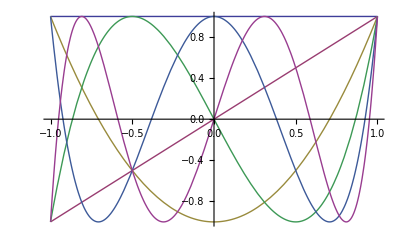

(π | 0 | 0 | 0
0 | π/2 | 0 | 0
0 | 0 | π/2 | 0
0 | 0 | 0 | π/2)

```mathematica
Table[ChebyshevT[n,x],{n,0,5}]
Plot[%,{x,-1,1}]
Table[Integrate[(1-x^2)^(-1/2)ChebyshevT[n,x]ChebyshevT[m,x],{x,-1,1}],{n,0,3},{m,0,3}]//MatrixForm
```

### C. Rewrite the QNM equation in terms of g(u), where u = rh/r.

Note that the relevant range of u = rh/r is [0,1].  The point u=0 is the spacetime boundary, while u=1 is the horizon.  Scale by an appropriate power of u so that the result is non-vanishing and non-singular at u=0.  For later convenience, express m in terms of the temperature T, and introduce a dimensionless rescaled spatial momentum k = q/(πT) and decay rate λ = i ω/(πT).  All redefinitions (of f, r, q, and ω) can be easily done in a single line using substitutions acting on QNMeqn. Try using PowerExpand and Simplify (and removal of irrelevant overall factors) to make your result look nice.  The derivative terms in your result (call it QNMeqn2) should equal (or be equivalent to) (-5+9 u^4-2 u λ) g'[u]+u (-1+u^4) g''[u].

```mathematica
QNMeqn2=L^6 m^(3/2)u^-7 QNMeqn/.r->rh/u/.f->(#^-4 g[rh/#]&)/.msub/.q->k π T/.ω->-I λ π T//PowerExpand//Simplify
```

(k^2 u+16 u^3-5 λ) g[u]+(-5+9 u^4-2 u λ) g'[u]+u (-1+u^4) g''[u]

### D. Approximate g as a linear combination of the first M+1 Chebyshev polynomials, linearly mapped onto the domain [0,1].

Pick some value for M which is more than 3 and less than 8.  Define a vector coeffs of your unknown expansion coefficients.  Define gsub as a substutution which replaces the function g by a pure function equal to the sum of the first M+1 Chebyshev’s with your unspecified expansion coefficients.

```mathematica
M=5;
gsub=g->Function[u,Sum[c[n] ChebyshevT[n,2u-1],{n,0,M}]]
coeffs=Table[c[n],{n,0,M}]
```

g→Function[u,∑_(n=0)^M c[n] ChebyshevT[n,2 u-1]]

{c[0],c[1],c[2],c[3],c[4],c[5]}

### E. Define appropriate Chebyshev (Gauss-Lobatto) grid points.

When working on the interval [-1,1], the Gauss-Lobatto grid points for an M+1 term Chebyshev series are given by cos(nπ/M), for n=0,...,M.  Linearly map these values onto the u domain of [0,1], and define a vector ugrid listing the resulting values.  For later convenience, evalute these values numerically.

```mathematica
ugrid=Table[1/2(1-Cos[n Pi/M]),{n,0,M}]//N
```

{0.,0.0954915,0.345492,0.654508,0.904508,1.}

### F. Plug the Chebyshev expansion into the QNM equation for g(u). Evaluate the resulting (truncated) QNM equation at each point on the Chebyshev grid.

Name the resulting list of equations QNMtrunc.

```mathematica
QNMtrunc=QNMeqn2/.gsub//Simplify
QNMtrunc/.u->ugrid
```

2 (-5+9 u^4-2 u λ) (c[1]+4 (-1+2 u) c[2]+3 (3-16 u+16 u^2) c[3]+4 (4-8 u+8 (-1+2 u)^3) c[4]+5 (1-12 (1-2 u)^2+16 (1-2 u)^4) c[5])+16 u (-1+u^4) (c[2]+6 (-1+2 u) c[3]+20 c[4]-96 u c[4]+96 u^2 c[4]-50 c[5]+420 u c[5]-960 u^2 c[5]+640 u^3 c[5])+(k^2 u+16 u^3-5 λ) (c[0]+(-1+2 u) c[1]+(1-8 u+8 u^2) c[2]+(-1+18 u-48 u^2+32 u^3) c[3]+(1-8 (1-2 u)^2+8 (1-2 u)^4) c[4]+(-5+10 u-20 (-1+2 u)^3+16 (-1+2 u)^5) c[5])

{0.+(0.-5 λ) (c[0]-1. c[1]+1. c[2]-1. c[3]+1. c[4]-1. c[5])-10. (c[1]-4. c[2]+9. c[3]-16. c[4]+25. c[5]),2 (-4.99925-0.190983 λ) (0.+c[1]-3.23607 c[2]+4.8541 c[3]-4. c[4])-1.52774 (c[2]-4.8541 c[3]+11.7082 c[4]-18.0902 c[5])+(0.013932+0.0954915 k^2-5 λ) (c[0]-0.809017 c[1]+0.309017 c[2]+0.309017 c[3]-0.809017 c[4]+1. c[5]),(0.65983+0.345492 k^2-5 λ) (c[0]-0.309017 c[1]-0.809017 c[2]+0.809017 c[3]+0.309017 c[4]-1. c[5])+2 (-4.87177-0.690983 λ) (c[1]-1.23607 c[2]-1.8541 c[3]+4. c[4]-1.249×10^-15 c[5])-5.4491 (c[2]-1.8541 c[3]-1.7082 c[4]+6.90983 c[5]),-8.55039 (c[2]+1.8541 c[3]-1.7082 c[4]-6.90983 c[5])+2 (-3.3484-1.30902 λ) (c[1]+1.23607 c[2]-1.8541 c[3]-4. c[4]-1.249×10^-15 c[5])+(4.48607+0.654508 k^2-5 λ) (c[0]+0.309017 c[1]-0.809017 c[2]-0.809017 c[3]+0.309017 c[4]+1. c[5]),2 (1.02411-1.80902 λ) (0.+c[1]+3.23607 c[2]+4.8541 c[3]+4. c[4])+(11.8402+0.904508 k^2-5 λ) (c[0]+0.809017 c[1]+0.309017 c[2]-0.309017 c[3]-0.809017 c[4]-1. c[5])-4.78527 (c[2]+4.8541 c[3]+11.7082 c[4]+18.0902 c[5]),0.+(16.+1. k^2-5 λ) (c[0]+1. c[1]+1. c[2]+1. c[3]+1. c[4]+1. c[5])+2 (4.-2. λ) (c[1]+4. c[2]+9. c[3]+16. c[4]+25. c[5])}

### G. The resulting equation, at each grid point, is a linear combination of the unknown expansion coefficients. Extract the coefficient q_ij which multiplies your j’th expansion coefficient in the equation for the i’th grid point. Assemble a matrix Q = ||q_ij||, such that the complete set of equations are Q.coeffs = 0.

Using the Mathematica function Coefficient, together with Map (or /@), is the simplest way to do this.  Note that the second argument to Coefficient can be a list of objects whose coefficients are desired, not just a single object. Verify explicitly that your result, in terms of Q, is in fact equivalent to the previous set of equations.

```mathematica
QNMmtx=Coefficient[#,coeffs]&/@(QNMtrunc/.u->ugrid)
QNMmtx.coeffs-(QNMtrunc/.u->ugrid)//Simplify//Chop
```

{{-5 λ,-10.+5. λ,40.-5. λ,-90.+5. λ,160.-5. λ,-250.+5. λ},{0.013932+0.0954915 k^2-5 λ,-10.0098-0.0772542 k^2+3.66312 λ,30.8324+0.0295085 k^2-0.309017 λ,-41.1137+0.0295085 k^2-3.39919 λ,22.0957-0.0772542 k^2+5.57295 λ,27.651+0.0954915 k^2-5. λ},{0.65983+0.345492 k^2-5 λ,-9.94744-0.106763 k^2+0.163119 λ,6.06076-0.279508 k^2+5.75329 λ,28.7025+0.279508 k^2-1.48278 λ,-29.4621+0.106763 k^2-7.07295 λ,-38.3122-0.345492 k^2+5. λ},{4.48607+0.654508 k^2-5 λ,-5.31054+0.202254 k^2-4.16312 λ,-20.4574-0.529508 k^2+0.809017 λ,-7.06603-0.529508 k^2+8.89919 λ,42.7793+0.202254 k^2+8.92705 λ,63.5678+0.654508 k^2-5. λ},{11.8402+0.904508 k^2-5 λ,11.6271+0.731763 k^2-7.66312 λ,5.50174+0.279508 k^2-13.2533 λ,-16.9447-0.279508 k^2-16.0172 λ,-57.4129-0.731763 k^2-10.4271 λ,-98.4065-0.904508 k^2+5. λ},{16.+1. k^2-5 λ,24.+1. k^2-9. λ,48.+1. k^2-21. λ,88.+1. k^2-41. λ,144.+1. k^2-69. λ,216.+1. k^2-105. λ}}

{0,0,0,0,0,0}

### H. Every element of Q is at most linear in λ. So Q = α - λ β for some matrices α and β (independent of λ), and the truncated QNM equations have the form α.coeffs = λ β.coeffs.

This is a generalized eigenvalue equation.  Extract the matrices α and β from Q.

```mathematica
α=QNMmtx/.λ->0
β=-Coefficient[QNMmtx,λ]
```

{{0,-10.,40.,-90.,160.,-250.},{0.013932+0.0954915 k^2,-10.0098-0.0772542 k^2,30.8324+0.0295085 k^2,-41.1137+0.0295085 k^2,22.0957-0.0772542 k^2,27.651+0.0954915 k^2},{0.65983+0.345492 k^2,-9.94744-0.106763 k^2,6.06076-0.279508 k^2,28.7025+0.279508 k^2,-29.4621+0.106763 k^2,-38.3122-0.345492 k^2},{4.48607+0.654508 k^2,-5.31054+0.202254 k^2,-20.4574-0.529508 k^2,-7.06603-0.529508 k^2,42.7793+0.202254 k^2,63.5678+0.654508 k^2},{11.8402+0.904508 k^2,11.6271+0.731763 k^2,5.50174+0.279508 k^2,-16.9447-0.279508 k^2,-57.4129-0.731763 k^2,-98.4065-0.904508 k^2},{16.+1. k^2,24.+1. k^2,48.+1. k^2,88.+1. k^2,144.+1. k^2,216.+1. k^2}}

{{5,-5.,5.,-5.,5.,-5.},{5,-3.66312,0.309017,3.39919,-5.57295,5.},{5,-0.163119,-5.75329,1.48278,7.07295,-5.},{5,4.16312,-0.809017,-8.89919,-8.92705,5.},{5,7.66312,13.2533,16.0172,10.4271,-5.},{5,9.,21.,41.,69.,105.}}

### I. Pick an O(1) value for k^2. Find the set of generalized eigenvalues {λ} which satisfy the truncated QNM equation.

Note that the function Eigenvalues can solve generalized eigenvalue problems.  For convenience, reverse the order of the list produced by Eigenvalues so that the smallest eigenvalues (in absolute value) are first.  These characterize the slowest modes of relaxation.

```mathematica
Eigenvalues[{α,β}/.k->0]//Reverse
```

{2.31955-2.20666 ⅈ,2.31955+2.20666 ⅈ,3.26418-0.852315 ⅈ,3.26418+0.852315 ⅈ,1.19905+3.66699 ⅈ,1.19905-3.66699 ⅈ}

### J. A formally equivalent procedure is to evaluate the determinant of Q, and then solve for the roots of the resulting polynomial equation in λ. This works well for very small values of M, but rapidly becomes computational problematic as M increases.

Why is this?

The determinant must be evaluated with an unknown (symbolic) value of λ.  This requires using a recursive definition of the determinant which generates M! terms.  As M increases, factorial growth in the computational complexity is a disaster.

### K. Now write a single Mathematica function which will take the truncation order M and the rescaled spatial momentum k as arguments, and produce the list of resulting (approximations) to the quasinormal mode decay rates. Explore the stability of your results with increasing M. How many terms are needed to obtain an accurate result for the lowest QNM frequency? How many for the second, third, ...? What is the rate of convergence with increasing M?

As the truncation order M increases, you will likely have increasing problems with numerical loss of precision.  This occurs because Mathematica “simplifies” expressions involving Chebyshev polynomials of known order, but symbolic argument, by substituting in the explicit polynomials. When the symbolic argument is subsequently replaced by an explicit numerical value, very large cancellations can occur, leading to loss of precision.  But if an expression involves a Chebyshev polynomial with a numerical argument, then Mathematica uses stable recursion relations to evaluate the polynomial, even for high orders, without major loss of precision.  To cope with this problem, there are two reasonable approaches:

1. Force Mathematica to use arbitrary precision arithmetic.  An easy way to do this is to define ugrid using N[expr,precision], with precision set to 30, 50, or more digits (depending on your target value of M).

2. Use your own temporary name for Chebyshev’s, and only substitute Mathematica’s ChebyshevT for your name after you have inserted numerical values for u.  The substitution which does this renaming must also reexpress first and second derivatives of your functions in terms standard Mathematica functions.  For this, the relation (d/dx)^m T_n(x) = n 2^(m-1)(m-1)! C_(n-m)^(m)(x), with C_(n-m)^(m)(x) a Gegenbauer polynomial, is convenient.  This approach is trickier, but faster, than option 1.

```mathematica
Clear[gsub,coeffs,ugrid,M,QNMroots];
gsub[M_]:=g:>Function[u,Sum[c[n] cheby[n,2u-1],{n,0,M}]];
ugrid[M_,prec_]:=Table[1/2(1-Cos[n Pi/M])//N[#,prec]&,{n,0,M}];
coeffs[M_]:=Table[c[n],{n,0,M}];
geneigs[mtx_]:=Eigenvalues[{mtx/.λ->0,-Coefficient[mtx,λ]}]//Reverse;
QNMroots[M_,kk_,prec_:MachinePrecision]:=geneigs[(Coefficient[#,coeffs[M]]&/@((QNMeqn2/.k->kk/.gsub[M]/.u->#)&/@ugrid[M,prec]))/.chebysub];
chebysub={Derivative[0,m_][cheby][n_,u_?NumberQ]->n 2^(m-1)(m-1)!GegenbauerC[n-m,m,u],
cheby[n_,u_?NumberQ]->ChebyshevT[n,u]};
```

```mathematica
QNMroots[5,0]
QNMroots[10,0]
QNMroots[15,0]
QNMroots[20,0]
QNMroots[25,0]
QNMroots[30,0]
QNMroots[35,0]
QNMroots[40,0]
```

{2.31955-2.20666 ⅈ,2.31955+2.20666 ⅈ,3.26418-0.852315 ⅈ,3.26418+0.852315 ⅈ,1.19905-3.66699 ⅈ,1.19905+3.66699 ⅈ}

{2.72974+3.1249 ⅈ,2.72974-3.1249 ⅈ,4.06469-3.41811 ⅈ,4.06469+3.41811 ⅈ,5.41647+0. ⅈ,5.09385-1.9446 ⅈ,5.09385+1.9446 ⅈ,2.84624+5.18343 ⅈ,2.84624-5.18343 ⅈ,1.64033-7.53751 ⅈ,1.64033+7.53751 ⅈ}

{2.7467-3.11945 ⅈ,2.7467+3.11945 ⅈ,4.61134-5.05565 ⅈ,4.61134+5.05565 ⅈ,5.98017+4.46557 ⅈ,5.98017-4.46557 ⅈ,7.39828-1.08969 ⅈ,7.39828+1.08969 ⅈ,6.97439-3.10506 ⅈ,6.97439+3.10506 ⅈ,4.33318+6.64024 ⅈ,4.33318-6.64024 ⅈ,3.45506-8.83787 ⅈ,3.45506+8.83787 ⅈ,2.13706-11.6104 ⅈ,2.13706+11.6104 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76414-5.16998 ⅈ,4.76414+5.16998 ⅈ,6.44495-6.58585 ⅈ,6.44495+6.58585 ⅈ,9.53017+0. ⅈ,9.32768+2.24186 ⅈ,9.32768-2.24186 ⅈ,7.98806+5.54074 ⅈ,7.98806-5.54074 ⅈ,8.87683+4.31691 ⅈ,8.87683-4.31691 ⅈ,5.76575-8.11084 ⅈ,5.76575+8.11084 ⅈ,5.04378-10.2321 ⅈ,5.04378+10.2321 ⅈ,4.07096+12.699 ⅈ,4.07096-12.699 ⅈ,2.64613+15.7849 ⅈ,2.64613-15.7849 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76607-7.19914 ⅈ,6.76607+7.19914 ⅈ,8.24153+7.8017 ⅈ,8.24153-7.8017 ⅈ,11.5706-1.15229 ⅈ,11.5706+1.15229 ⅈ,11.2274-3.41634 ⅈ,11.2274+3.41634 ⅈ,7.22446+9.57606 ⅈ,7.22446-9.57606 ⅈ,10.0471-6.58591 ⅈ,10.0471+6.58591 ⅈ,10.7815+5.5952 ⅈ,10.7815-5.5952 ⅈ,6.5584-11.6459 ⅈ,6.5584+11.6459 ⅈ,5.73705-13.9804 ⅈ,5.73705+13.9804 ⅈ,4.67497-16.6772 ⅈ,4.67497+16.6772 ⅈ,3.15485-20.0238 ⅈ,3.15485+20.0238 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76957+7.18791 ⅈ,6.76957-7.18791 ⅈ,8.66937+9.18739 ⅈ,8.66937-9.18739 ⅈ,10.1199-8.80206 ⅈ,10.1199+8.80206 ⅈ,13.7081+0. ⅈ,13.5543-2.32983 ⅈ,13.5543+2.32983 ⅈ,13.1086-4.59857 ⅈ,13.1086+4.59857 ⅈ,8.67711-10.9969 ⅈ,8.67711+10.9969 ⅈ,12.2117-7.51662 ⅈ,12.2117+7.51662 ⅈ,12.6435-7.01956 ⅈ,12.6435+7.01956 ⅈ,8.04068-13.0665 ⅈ,8.04068+13.0665 ⅈ,7.30503+15.3251 ⅈ,7.30503-15.3251 ⅈ,6.40838+17.842 ⅈ,6.40838-17.842 ⅈ,5.26644-20.7348 ⅈ,5.26644+20.7348 ⅈ,3.65972-24.3074 ⅈ,3.65972+24.3074 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357-5.16952 ⅈ,4.76357+5.16952 ⅈ,6.76956+7.18793 ⅈ,6.76956-7.18793 ⅈ,8.77274-9.19703 ⅈ,8.77274+9.19703 ⅈ,10.5028-10.8618 ⅈ,10.5028+10.8618 ⅈ,12.1068+9.82778 ⅈ,12.1068-9.82778 ⅈ,15.7852+1.08824 ⅈ,15.7852-1.08824 ⅈ,15.4626+3.60305 ⅈ,15.4626-3.60305 ⅈ,10.0859+12.4215 ⅈ,10.0859-12.4215 ⅈ,15.0357+5.70697 ⅈ,15.0357-5.70697 ⅈ,13.9251-8.1894 ⅈ,13.9251+8.1894 ⅈ,9.50594+14.4893 ⅈ,9.50594-14.4893 ⅈ,14.9726-8.76421 ⅈ,14.9726+8.76421 ⅈ,8.82545-16.6991 ⅈ,8.82545+16.6991 ⅈ,8.0254-19.1092 ⅈ,8.0254+19.1092 ⅈ,7.06073-21.7854 ⅈ,7.06073+21.7854 ⅈ,5.84633-24.8504 ⅈ,5.84633+24.8504 ⅈ,4.15992-28.6241 ⅈ,4.15992+28.6241 ⅈ}

{2.74668-3.11945 ⅈ,2.74668+3.11945 ⅈ,4.76357+5.16952 ⅈ,4.76357-5.16952 ⅈ,6.76956-7.18793 ⅈ,6.76956+7.18793 ⅈ,8.77229-9.1971 ⅈ,8.77229+9.1971 ⅈ,10.7645-11.1785 ⅈ,10.7645+11.1785 ⅈ,16.4397-1.91037 ⅈ,16.4397+1.91037 ⅈ,15.5569-5.71412 ⅈ,15.5569+5.71412 ⅈ,13.9317-9.42653 ⅈ,13.9317+9.42653 ⅈ,12.0877-12.2919 ⅈ,12.0877+12.2919 ⅈ,11.5409+13.906 ⅈ,11.5409-13.906 ⅈ,15.16-11.4589 ⅈ,15.16+11.4589 ⅈ,10.9629+15.9115 ⅈ,10.9629-15.9115 ⅈ,19.8856+0. ⅈ,19.2418-5.80201 ⅈ,19.2418+5.80201 ⅈ,18.0829+10.2769 ⅈ,18.0829-10.2769 ⅈ,10.319-18.0888 ⅈ,10.319+18.0888 ⅈ,9.58276-20.428 ⅈ,9.58276+20.428 ⅈ,8.72371-22.9729 ⅈ,8.72371+22.9729 ⅈ,7.69684+25.7911 ⅈ,7.69684-25.7911 ⅈ,6.4159-29.0108 ⅈ,6.4159+29.0108 ⅈ,4.65546+32.9662 ⅈ,4.65546-32.9662 ⅈ}

λ_1=2.74668 ± 3.11945 i, is stable by M=18.  λ_2=4.76357 ± 5.16952 i, is stable by M=25.  λ_3=6.76956 ± 7.18793 i, is stable by M=30.  Convergence, for a given eigenvalue, is exponential with increasing M (until numerical loss of precision becomes the dominant error).

### L. Still going strong?

Compare your results with those in the table at the end of hep-th/0506184. (Note that Kovtun and Starinets scaled their spatial momenta and frequencies by 2πT, not πT.)  Are your results consistent with theirs?  Are all their digits shown accurate?

```mathematica
QNMroots[20,2]/2
QNMroots[30,2]/2
QNMroots[40,2]/2
QNMroots[50,2]/2
```

{1.26733-1.95433 ⅈ,1.26733+1.95433 ⅈ,2.29762-2.88055 ⅈ,2.29762+2.88055 ⅈ,3.28676+3.42224 ⅈ,3.28676-3.42224 ⅈ,4.90467+0. ⅈ,4.80115-1.1355 ⅈ,4.80115+1.1355 ⅈ,4.08038-2.87604 ⅈ,4.08038+2.87604 ⅈ,2.85909-4.10326 ⅈ,2.85909+4.10326 ⅈ,4.54447-2.17694 ⅈ,4.54447+2.17694 ⅈ,2.51209-5.15318 ⅈ,2.51209+5.15318 ⅈ,2.03039+6.38349 ⅈ,2.03039-6.38349 ⅈ,1.32175+7.92273 ⅈ,1.32175-7.92273 ⅈ}

{1.26733+1.95433 ⅈ,1.26733-1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31492-3.83663 ⅈ,3.31492+3.83663 ⅈ,4.29869-4.76325 ⅈ,4.29869+4.76325 ⅈ,5.17641-4.4928 ⅈ,5.17641+4.4928 ⅈ,6.97826+0. ⅈ,6.90052+1.17343 ⅈ,6.90052-1.17343 ⅈ,4.33258-5.51855 ⅈ,4.33258+5.51855 ⅈ,6.67644+2.31414 ⅈ,6.67644-2.31414 ⅈ,6.14586+3.90892 ⅈ,6.14586-3.90892 ⅈ,6.41901-3.44797 ⅈ,6.41901+3.44797 ⅈ,4.01177+6.56005 ⅈ,4.01177-6.56005 ⅈ,3.64644-7.6878 ⅈ,3.64644+7.6878 ⅈ,3.20027+8.94462 ⅈ,3.20027-8.94462 ⅈ,2.6311+10.3893 ⅈ,2.6311-10.3893 ⅈ,1.82933-12.1737 ⅈ,1.82933+12.1737 ⅈ}

{1.26733-1.95433 ⅈ,1.26733+1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31491-3.83663 ⅈ,3.31491+3.83663 ⅈ,4.32573-4.80734 ⅈ,4.32573+4.80734 ⅈ,5.32281-5.77164 ⅈ,5.32281+5.77164 ⅈ,7.97778-1.00564 ⅈ,7.97778+1.00564 ⅈ,7.57704+2.9804 ⅈ,7.57704-2.9804 ⅈ,6.79643-4.85091 ⅈ,6.79643+4.85091 ⅈ,6.09001-6.31639 ⅈ,6.09001+6.31639 ⅈ,5.78218+6.96564 ⅈ,5.78218-6.96564 ⅈ,5.47346-7.97485 ⅈ,5.47346+7.97485 ⅈ,7.88854-5.93237 ⅈ,7.88854+5.93237 ⅈ,10.4133+0. ⅈ,5.15362+9.06436 ⅈ,5.15362-9.06436 ⅈ,10.0476-2.83131 ⅈ,10.0476+2.83131 ⅈ,9.27149-5.09764 ⅈ,9.27149+5.09764 ⅈ,4.787+10.2331 ⅈ,4.787-10.2331 ⅈ,4.35872+11.5046 ⅈ,4.35872-11.5046 ⅈ,3.84636-12.9127 ⅈ,3.84636+12.9127 ⅈ,3.20683-14.5214 ⅈ,3.20683+14.5214 ⅈ,2.32749-16.498 ⅈ,2.32749+16.498 ⅈ}

{1.26733-1.95433 ⅈ,1.26733+1.95433 ⅈ,2.29796-2.88026 ⅈ,2.29796+2.88026 ⅈ,3.31491-3.83663 ⅈ,3.31491+3.83663 ⅈ,4.32614+4.80749 ⅈ,4.32614-4.80749 ⅈ,7.31975-0.824714 ⅈ,7.31975+0.824714 ⅈ,7.06074-2.44886 ⅈ,7.06074+2.44886 ⅈ,6.55015+4.00009 ⅈ,6.55015-4.00009 ⅈ,5.30971-5.88031 ⅈ,5.30971+5.88031 ⅈ,5.78135+5.43541 ⅈ,5.78135-5.43541 ⅈ,5.63395-6.93623 ⅈ,5.63395+6.93623 ⅈ,5.79451+7.9825 ⅈ,5.79451-7.9825 ⅈ,5.97303+9.09165 ⅈ,5.97303-9.09165 ⅈ,6.16151-10.2561 ⅈ,6.16151+10.2561 ⅈ,6.21821-11.5354 ⅈ,6.21821+11.5354 ⅈ,7.36826-11.2692 ⅈ,7.36826+11.2692 ⅈ,5.92364-12.7832 ⅈ,5.92364+12.7832 ⅈ,10.0984-10.7596 ⅈ,10.0984+10.7596 ⅈ,5.51261+14.0639 ⅈ,5.51261-14.0639 ⅈ,12.8027-9.54365 ⅈ,12.8027+9.54365 ⅈ,5.03152-15.4521 ⅈ,5.03152+15.4521 ⅈ,15.1601+7.29312 ⅈ,15.1601-7.29312 ⅈ,16.8294+3.9721 ⅈ,16.8294-3.9721 ⅈ,17.4429+0. ⅈ,4.46328-16.984 ⅈ,4.46328+16.984 ⅈ,3.7637+18.7284 ⅈ,3.7637-18.7284 ⅈ,2.8168-20.8657 ⅈ,2.8168+20.8657 ⅈ}

First three (complex conjugate pairs) of eigenvalues compare fine with Kovtun & Starinets.  Beyond that, it looks like precision loss (and/or the spectral truncation) is corrupting results.  To see which, we can recompute with extended precision.  This shows that precision loss was a problem in the above (machine precision) results for higher quasinormal modes.  With M=50, and extended precision, results agree nicely with Kovtun & Starinets:

```mathematica
QNMroots[20,2,30]/2
QNMroots[30,2,30]/2
QNMroots[40,2,30]/2
QNMroots[50,2,30]/2
```

{1.26732727539794909501493-1.95433087146849939403639 ⅈ,1.26732727539794909501493+1.95433087146849939403639 ⅈ,2.29761756685275515093336-2.88055122207291754672557 ⅈ,2.29761756685275515093336+2.88055122207291754672557 ⅈ,3.28676434116845335401791-3.42223653431144000124448 ⅈ,3.28676434116845335401791+3.42223653431144000124448 ⅈ,4.90466835715088471396312,4.80114616098510634137391-1.13550143915216746267978 ⅈ,4.80114616098510634137391+1.13550143915216746267978 ⅈ,4.08038070680847678643255-2.87603944605452928566832 ⅈ,4.08038070680847678643255+2.87603944605452928566832 ⅈ,2.85908821355954298193676-4.10325841764087695087471 ⅈ,2.85908821355954298193676+4.10325841764087695087471 ⅈ,4.54446693516245840068674-2.17694126979147269867136 ⅈ,4.54446693516245840068674+2.17694126979147269867136 ⅈ,2.51209356565227021831607+5.15318262572532319104793 ⅈ,2.51209356565227021831607-5.15318262572532319104793 ⅈ,2.03039029217053862928468-6.38349038394510046739998 ⅈ,2.03039029217053862928468+6.38349038394510046739998 ⅈ,1.32175033069290950218924-7.92273092096611108343867 ⅈ,1.32175033069290950218924+7.92273092096611108343867 ⅈ}

{1.26732726341707022709571-1.95433088379041284579575 ⅈ,1.26732726341707022709571+1.95433088379041284579575 ⅈ,2.29795704580093138202795-2.88026256539204171109936 ⅈ,2.29795704580093138202795+2.88026256539204171109936 ⅈ,3.3149214275881362320001+3.83663374715934510837485 ⅈ,3.3149214275881362320001-3.83663374715934510837485 ⅈ,4.29868897203904364094865-4.76326229245926411731277 ⅈ,4.29868897203904364094865+4.76326229245926411731277 ⅈ,5.17640457243705272614907-4.49275552765307162808003 ⅈ,5.17640457243705272614907+4.49275552765307162808003 ⅈ,6.97832850856632290729225,6.90047752634971414497686-1.17335992617744338759073 ⅈ,6.90047752634971414497686+1.17335992617744338759073 ⅈ,4.33257752582161683271013-5.51855685696722351569382 ⅈ,4.33257752582161683271013+5.51855685696722351569382 ⅈ,6.67642237558874484542821-2.3142467052385892304666 ⅈ,6.67642237558874484542821+2.3142467052385892304666 ⅈ,6.14583557497189210274538-3.90908788002427715958766 ⅈ,6.14583557497189210274538+3.90908788002427715958766 ⅈ,6.41906630415306720734091-3.44777754366724460507136 ⅈ,6.41906630415306720734091+3.44777754366724460507136 ⅈ,4.01177118168848649999511-6.56004997171867056358655 ⅈ,4.01177118168848649999511+6.56004997171867056358655 ⅈ,3.64644404726185372615092-7.6877959604241052535309 ⅈ,3.64644404726185372615092+7.6877959604241052535309 ⅈ,3.20026863249551252201408-8.94461737567688882516876 ⅈ,3.20026863249551252201408+8.94461737567688882516876 ⅈ,2.63109908459046696624944-10.3892530498275681127835 ⅈ,2.63109908459046696624944+10.3892530498275681127835 ⅈ,1.82933317386237577407388-12.1737167197133827679339 ⅈ,1.82933317386237577407388+12.1737167197133827679339 ⅈ}

{1.26732726341706410285085-1.95433088379042054659143 ⅈ,1.26732726341706410285085+1.95433088379042054659143 ⅈ,2.29795704651987263755697-2.88026256484964260639559 ⅈ,2.29795704651987263755697+2.88026256484964260639559 ⅈ,3.31490716032855514556195-3.83663222293320737893068 ⅈ,3.31490716032855514556195+3.83663222293320737893068 ⅈ,4.32587111939003429551884-4.80739193756078967171886 ⅈ,4.32587111939003429551884+4.80739193756078967171886 ⅈ,5.33221413277099184042022-5.7881080772495501073425 ⅈ,5.33221413277099184042022+5.7881080772495501073425 ⅈ,6.23194099793305973054509-6.16849707769900431021922 ⅈ,6.23194099793305973054509+6.16849707769900431021922 ⅈ,7.12005200567218969490657-5.5016151186086196449163 ⅈ,7.12005200567218969490657+5.5016151186086196449163 ⅈ,5.74646167539594221332271-6.96831223777301132714608 ⅈ,5.74646167539594221332271+6.96831223777301132714608 ⅈ,9.06538064548302058265807,9.00384931924750504514584-1.19449118405738807003274 ⅈ,9.00384931924750504514584+1.19449118405738807003274 ⅈ,8.82313180810857460692574-2.36582564173018046870326 ⅈ,8.82313180810857460692574+2.36582564173018046870326 ⅈ,8.52973800537671901718509-3.49668895118990730854232 ⅈ,8.52973800537671901718509+3.49668895118990730854232 ⅈ,8.04101818195526317377824-4.64641060233684842092459 ⅈ,8.04101818195526317377824+4.64641060233684842092459 ⅈ,5.47262157812776319293572-7.97720442931653159505922 ⅈ,5.47262157812776319293572+7.97720442931653159505922 ⅈ,8.60004840342213326724092-5.0979365703575990858546 ⅈ,8.60004840342213326724092+5.0979365703575990858546 ⅈ,5.1537153278543227534375-9.06449423533830060645489 ⅈ,5.1537153278543227534375+9.06449423533830060645489 ⅈ,4.78701239261060995396637-10.2330855128271748561702 ⅈ,4.78701239261060995396637+10.2330855128271748561702 ⅈ,4.35871782515072154066524-11.5045576861686066798277 ⅈ,4.35871782515072154066524+11.5045576861686066798277 ⅈ,3.8463563732010344227409-12.9126675154174256133618 ⅈ,3.8463563732010344227409+12.9126675154174256133618 ⅈ,3.20682844844889005523563-14.5214170021390225642655 ⅈ,3.20682844844889005523563+14.5214170021390225642655 ⅈ,2.32749050995697764350418-16.4979880731192637667881 ⅈ,2.32749050995697764350418+16.4979880731192637667881 ⅈ}

{1.2673272634170641028504-1.9543308837904205465965 ⅈ,1.2673272634170641028504+1.9543308837904205465965 ⅈ,2.2979570465198732580397-2.8802625648496418618889 ⅈ,2.2979570465198732580397+2.8802625648496418618889 ⅈ,3.31490716028999410921-3.8366322229339033238867 ⅈ,3.31490716028999410921+3.8366322229339033238867 ⅈ,4.3258713695497287327082-4.8073923430520995115796 ⅈ,4.3258713695497287327082+4.8073923430520995115796 ⅈ,5.3336221975535519220457-5.7861818912709116150608 ⅈ,5.3336221975535519220457+5.7861818912709116150608 ⅈ,6.3395117553496663341352-6.7699664849888459193064 ⅈ,6.3395117553496663341352+6.7699664849888459193064 ⅈ,7.2891201724253418070118-7.6436358931136996424779 ⅈ,7.2891201724253418070118+7.6436358931136996424779 ⅈ,8.1476244454176590960419+7.2074124688846377112797 ⅈ,8.1476244454176590960419-7.2074124688846377112797 ⅈ,7.1866218365554651454854-8.370018298292127177804 ⅈ,7.1866218365554651454854+8.370018298292127177804 ⅈ,9.0612813129323656726088-6.5129292089898935022211 ⅈ,9.0612813129323656726088+6.5129292089898935022211 ⅈ,11.159871053219510341344,11.108984817268606675077-1.2081126953137639077302 ⅈ,11.108984817268606675077+1.2081126953137639077302 ⅈ,10.958590804337400716423-2.4003077953881611219467 ⅈ,10.958590804337400716423+2.4003077953881611219467 ⅈ,10.715319750572887863789-3.5615222737245136798517 ⅈ,10.715319750572887863789+3.5615222737245136798517 ⅈ,10.383117598569138886099-4.6736300751282935387362 ⅈ,10.383117598569138886099+4.6736300751282935387362 ⅈ,9.8736698399962991607425-5.6946925348443161421346 ⅈ,9.8736698399962991607425+5.6946925348443161421346 ⅈ,6.9194848565687035645115-9.3990239853311032730451 ⅈ,6.9194848565687035645115+9.3990239853311032730451 ⅈ,6.625520993493094136787-10.463753513702579864319 ⅈ,6.625520993493094136787+10.463753513702579864319 ⅈ,10.955917286813711469537+6.5056149972380351788199 ⅈ,10.955917286813711469537-6.5056149972380351788199 ⅈ,6.2981674545244864756512-11.588050634927493026915 ⅈ,6.2981674545244864756512+11.588050634927493026915 ⅈ,5.930442939843775141294-12.783002271964244293096 ⅈ,5.930442939843775141294+12.783002271964244293096 ⅈ,5.5128969404888024452163-14.06366902269840460516 ⅈ,5.5128969404888024452163+14.06366902269840460516 ⅈ,5.0315193601522567500402-15.452041926202420740522 ⅈ,5.0315193601522567500402+15.452041926202420740522 ⅈ,4.4632752538111981233638-16.983984248800832200989 ⅈ,4.4632752538111981233638+16.983984248800832200989 ⅈ,3.763699819521768843262-18.728362287602982932335 ⅈ,3.763699819521768843262+18.728362287602982932335 ⅈ,2.8168022730823911457264-20.865663579304468771443 ⅈ,2.8168022730823911457264+20.865663579304468771443 ⅈ}